```mathematica
(* processing selection sort times *)
data = Import["/Users/john/structures/assignment2/quick.csv", "CSV"];
wordCounts = data[[All, 1]];
comparisons = data[[All, 2]];
swaps = data[[All, 3]];
times = data[[All, 4]];
```

15.0579+0.00167117 words-2.92128×10^-9 words^2

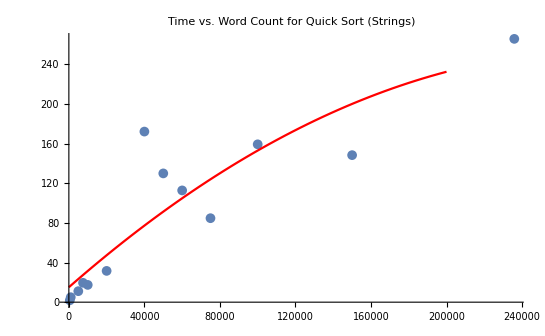

Set::write: Tag List in {11984, 180569, 2241717, 3708027, 396732, 5859588, 875184, 5105, 86458, 1078086, 1298379, 120581, 1721187}[words_] is Protected.

-92283.5+24.8823 words

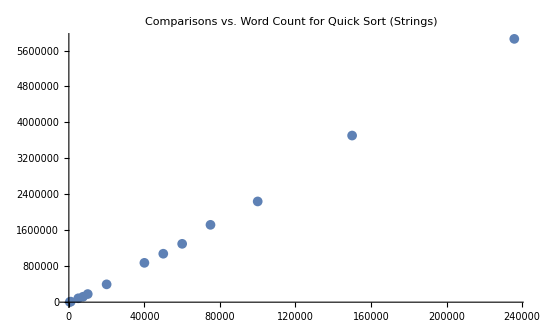

```mathematica
time[words_] = Fit[Transpose[{wordCounts, times}], {1, words, words^2}, words]

Show[ListPlot[Transpose[{wordCounts, times}]], Plot[time[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Time vs. Word Count for Quick Sort (Strings)"]

comparisons[words_] = Fit[Transpose[{wordCounts, comparisons}], {1, words}, words]

Show[ListPlot[Transpose[{wordCounts, comparisons}]], Plot[comparisons[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Comparisons vs. Word Count for Quick Sort (Strings)"]
```